```mathematica
ClearAll["Global`*"]
```

```mathematica
f0ToIOR[f0_]=(√f0+1)/(1-√f0);
IORtoF0[tIOR_,iIOR_]=((tIOR-iIOR)/(tIOR+iIOR))^2;
```

```mathematica
data=Table[{x,IORtoF0[f0ToIOR[x],1.5]},{x,0.052,0.999999999999,0.00001}];
```

```mathematica
poly=Fit[data,{1,x,x^2,x^3},x]
poly=FullSimplify[poly]
```

-0.0285998+0.346479 x+0.941892 x^2-0.263008 x^3

-0.0285998+x (0.346479+(0.941892-0.263008 x) x)

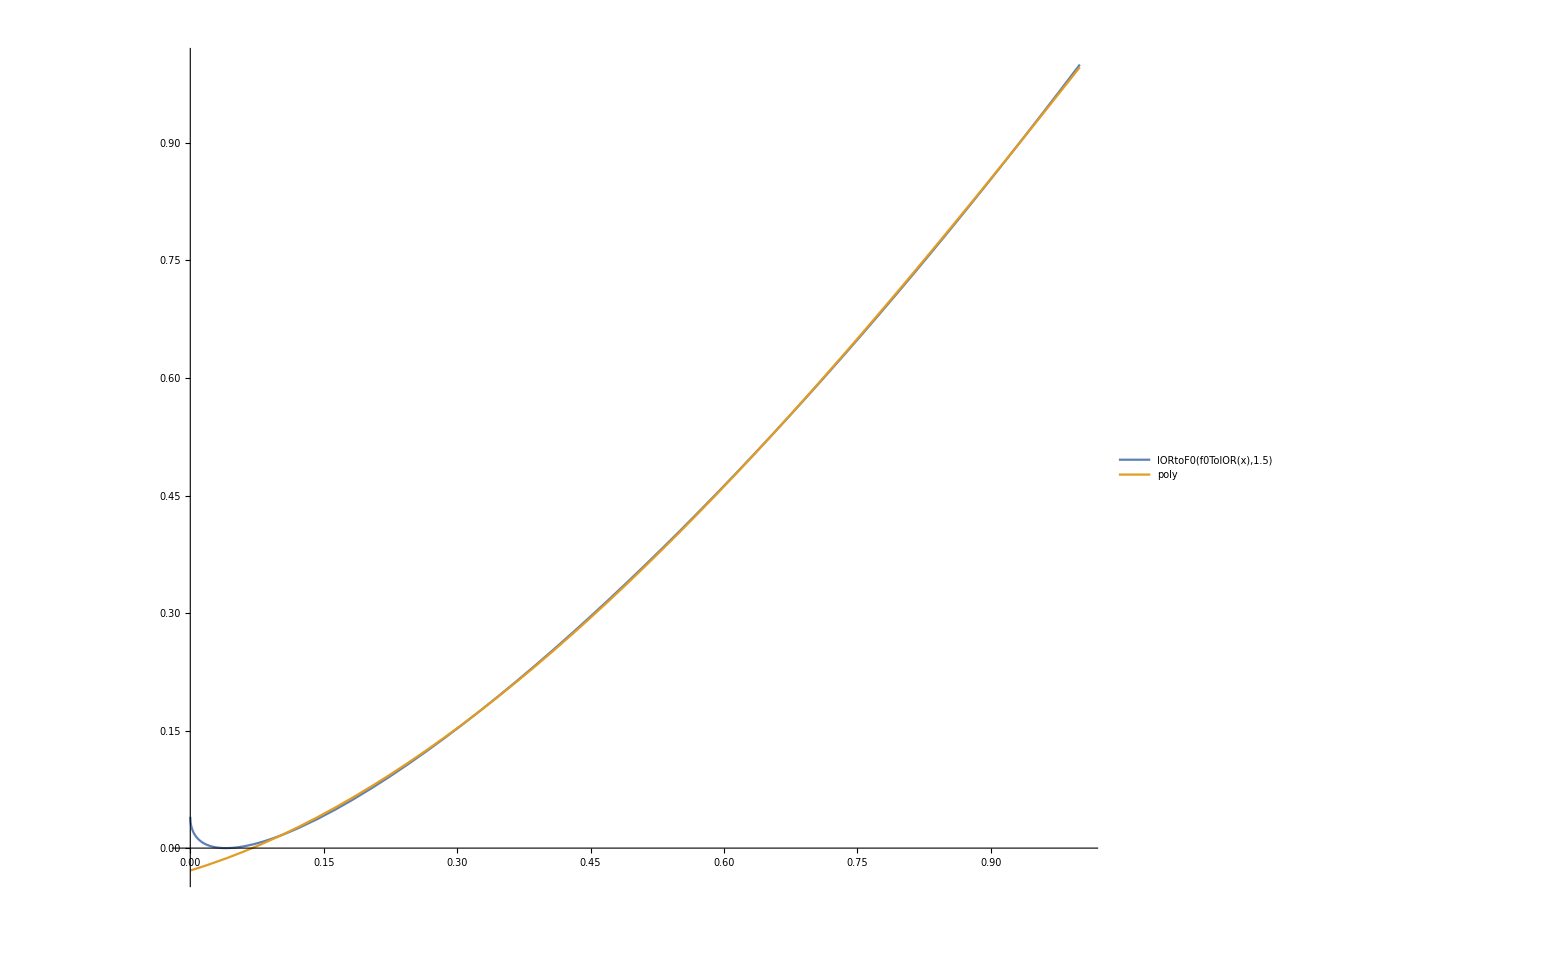

```mathematica
Plot[{IORtoF0[f0ToIOR[x],1.5],poly},{x,0,1},ImageSize->{1920,1080},PlotLegends->"Expressions"]
```

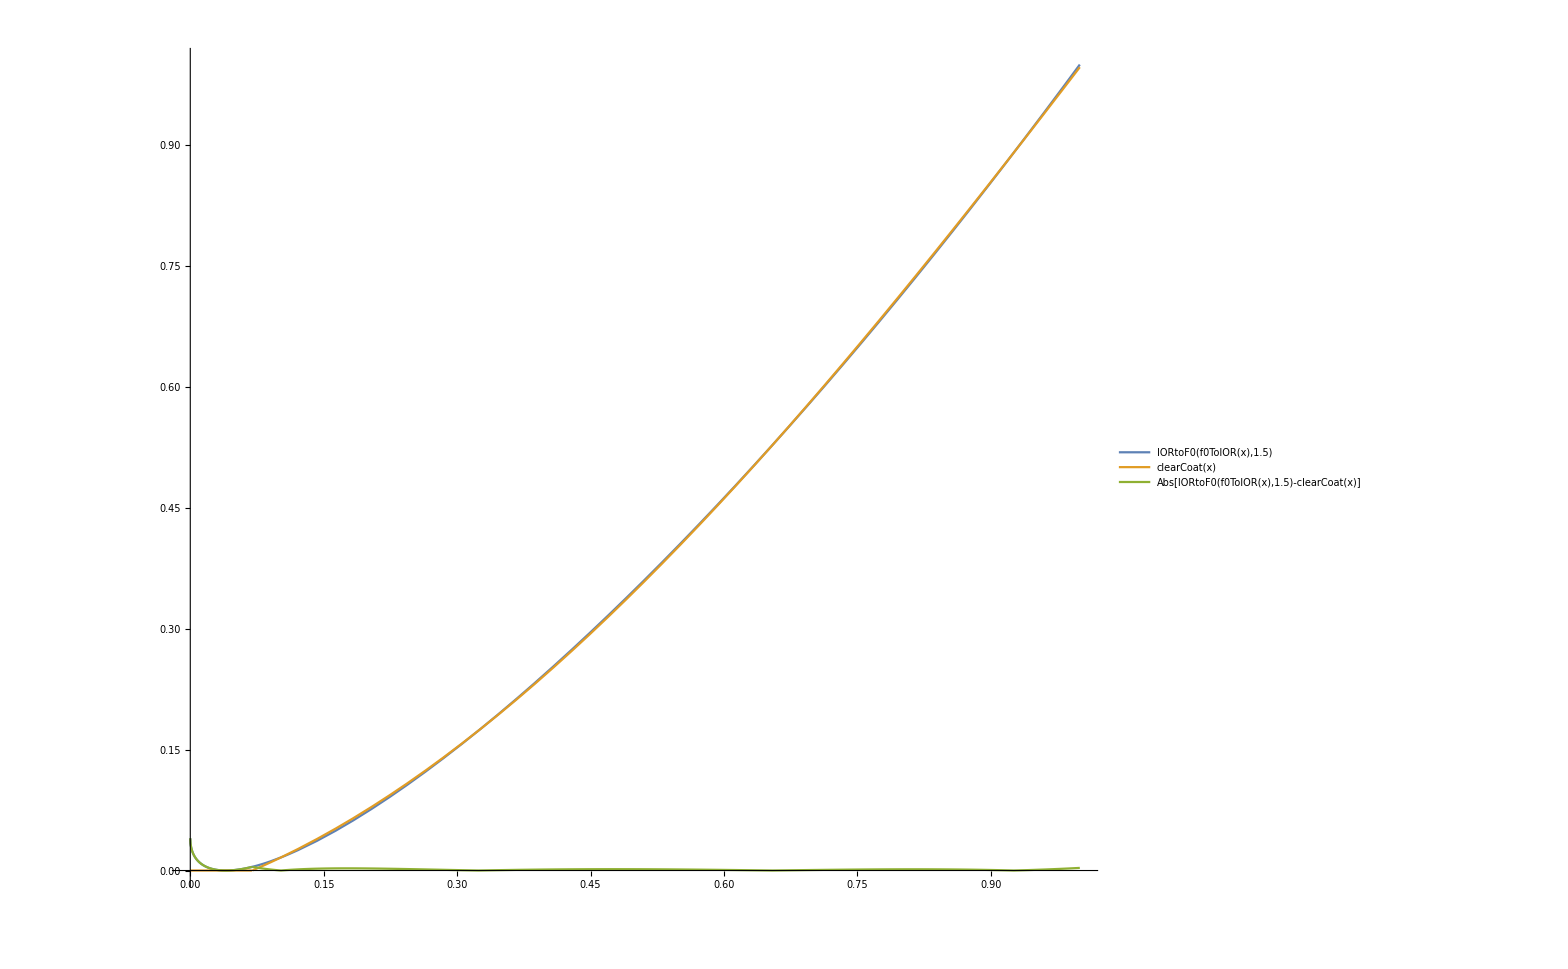

```mathematica
clearCoat[x_]=Clip[poly,{0,1}];
Plot[{IORtoF0[f0ToIOR[x],1.5],clearCoat[x],Abs[IORtoF0[f0ToIOR[x],1.5]-clearCoat[x]]},{x,0,1},ImageSize->{1920,1080},PlotLegends->"Expressions"]
```